```mathematica
(* 

 Compares OPAL and Astra initial distributions
   

 	
 *)

ClearAll[];NASTRA=200000; NOPAL=NASTRA;
SetDirectory["/Users/adelmann/svnwork/OPAL/opal-Doc/Notes/OPAL-vali-note/somedata"];

astra=OpenRead["Q200pC_th0p249um_XYrms275um_Tfwhm9p9ps_rf0p7ps_200k.ini"];
ASTRA=ReadList[astra,Table[Number,{i,1,10}]];

xASTRA = Table[ASTRA⟦i,1⟧,{i,1,NASTRA}];
yASTRA = Table[ASTRA⟦i,2⟧,{i,1,NASTRA}];
zASTRA = Table[ASTRA⟦i,3⟧,{i,1,NASTRA}];
pxASTRA = Table[ASTRA⟦i,4⟧,{i,1,NASTRA}];
pyASTRA = Table[ASTRA⟦i,5⟧,{i,1,NASTRA}];
pzASTRA = Table[ASTRA⟦i,6⟧,{i,1,NASTRA}];
```

```mathematica
opal=OpenRead["dist.dat"];

OPAL=ReadList[opal,Table[Number,{i,1,6}]];

xOPAL= Table[OPAL⟦i,1⟧,{i,1,NOPAL}];
yOPAL= Table[OPAL⟦i,2⟧,{i,1,NOPAL}];
zOPAL= Table[10^(-12)OPAL⟦i,3⟧,{i,1,NOPAL}];
```

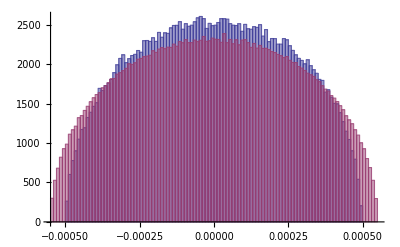

```mathematica
Histogram[{xOPAL,xASTRA}]   
Export["opal-astra-xic.pdf",%];
```

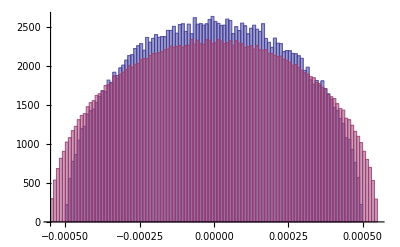

```mathematica
Histogram[{yOPAL,yASTRA}]
Export["opal-astra-yic.pdf",%];
```

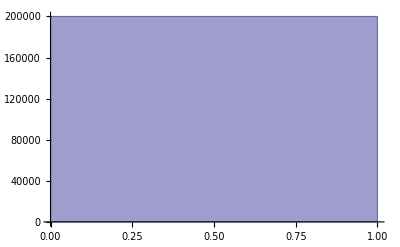

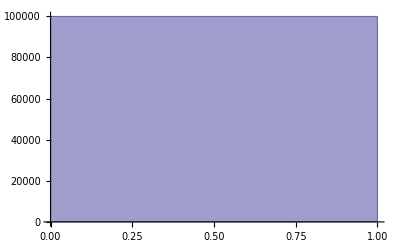

```mathematica
Histogram[{zASTRA}]
Histogram[{zOPAL}]
```

```mathematica
pxOPAL= Table[OPAL⟦i,4⟧,{i,1,NOPAL}];
```

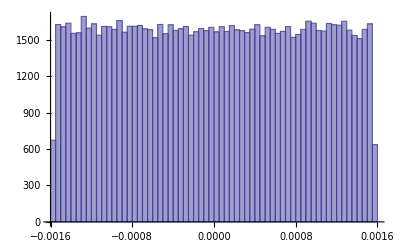

```mathematica
Histogram[{pxOPAL}]
```

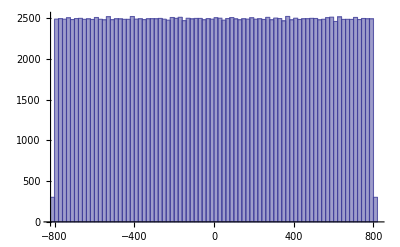

```mathematica
Histogram[{pxASTRA}]
```